# FindRandomGridMazeSolution

Find a solution to a random maze

## Definition

```mathematica
PositiveIntegerQ//ClearAll
PositiveIntegerQ[n_]:=And@@{IntegerQ[n],TrueQ[n∈PositiveIntegers]}
```

```mathematica
ClearAll[FindRandomGridMazeSolution]
```

```mathematica
FindRandomGridMazeSolution::usage="FindRandomGridMazeSolution[{m,n}] finds a solution and other data for a random grid maze of size m by n.";
FindRandomGridMazeSolution[{m1_?PositiveIntegerQ /;!(m1<=1)(*equivalent to n>1. The reason I impose this constraint is the graph needs to be big enough to take away edges and still have edges. GridGraph[{1,1}] has no edges.*),n1_?PositiveIntegerQ/;!(n1<=1)(*equivalent to n>1*)}]:=Module[{start,end,g,maze,m,solvedmaze,shortestPath,shortestPathSubgraph,deadEnds,deadEndsCount,treeOutline},g=GridGraph[{m1,n1}];m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g]];maze=m;
start=1(*First@VertexList[m]*);end=m1*n1(*Last@VertexList[m]*) (*We are only removing edges, not vertices. The last vertex will always be the product of m and n.*);solvedmaze=HighlightGraph[m,PathGraph@(shortestPath=FindShortestPath[m,start,end])];(*tree=GraphTree[maze];treeDepth=TreeDepth[tree];
treeLeaves=TreeLeaves[tree];
treeLeafCount=TreeLeafCount[tree];
treeSize=TreeSize[tree];*)
(*deadEnds=Complement[TreeLevel[tree,{-1}->"Data"],{end}];deadEndsCount=Length@deadEnds;treeOutline=TreeOutline[tree];*)shortestPathSubgraph=Subgraph[maze,shortestPath];<|"start"->start,"end"->end,"maze"->maze,"solved-maze"->solvedmaze,"shortest-path"->Iconize[shortestPath,"shortest-path"],"distance"->GraphDistance[m,start,end],"start"->start,"end"->end,"shortest-path-subgraph"->shortestPathSubgraph(*"tree"->tree,"tree-depth"->treeDepth,"tree-leaves"->treeLeaves,"tree-leaf-count"->treeLeafCount,"tree-size"->treeSize*)(*"dead-ends"->deadEnds,"dead-ends-count"->deadEndsCount,"tree-outline"->treeOutline*)|>]
```

## Documentation

### Usage

FindRandomGridMazeSolution[{m,n}]

finds a solution to a random maze of size m by n.

### Details & Options

How does this compare with https://resources.wolframcloud.com/FunctionRepository/resources/RandomMaze/ using the option "ShowSolution"-> True? 
Can you make an example comparing the two functions?
If the functionalities mainly overlap, we may reject this submission in favor of the existing resource function, unless you can show significant advantages in performance or functionality for your function.

## Examples

### Basic Examples

Be sure to use delimiters between independent examples. I have added some below.

Solve a 3 by 3 maze:

```mathematica
FindRandomGridMazeSolution[{3,3}]
```

-Graphics-

Solve a 5 by 5 maze:

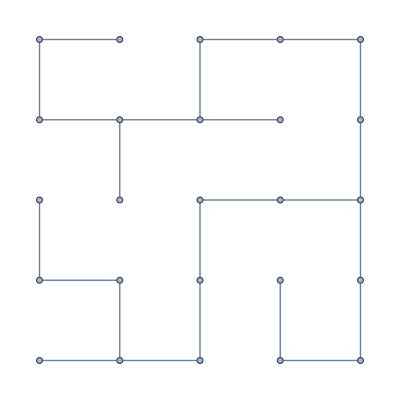
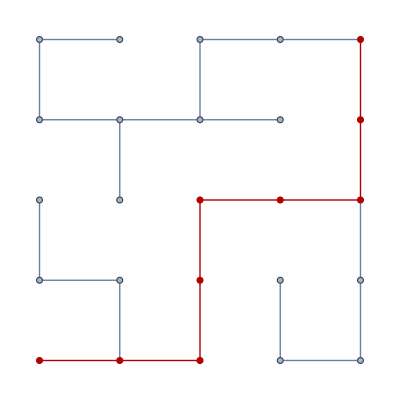
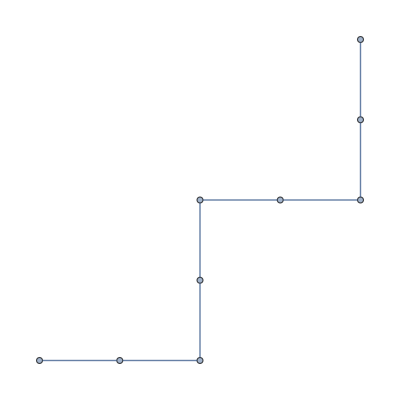
<|start→1,end→25,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→8,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{5,5}]
```

Solve a 10 by 10 maze:

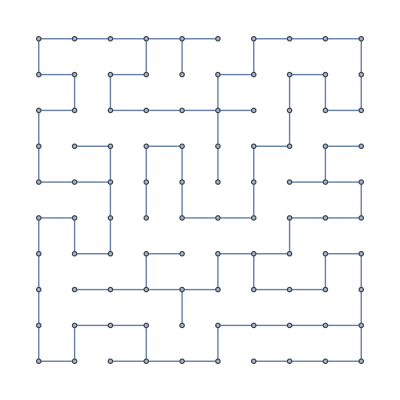
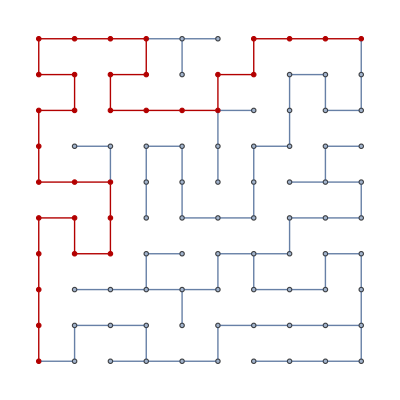
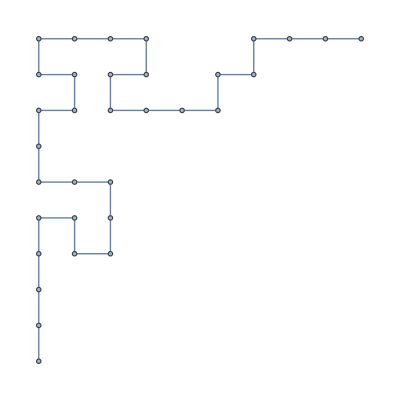
<|start→1,end→100,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→32,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{10,10}]
```

Solve a 15 by 15 maze:

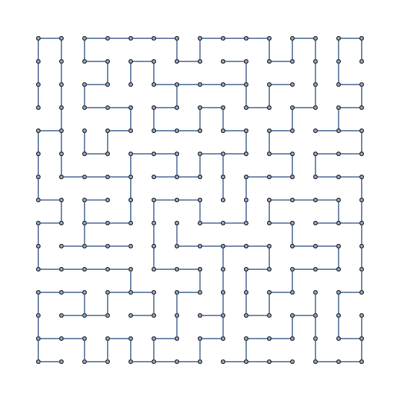
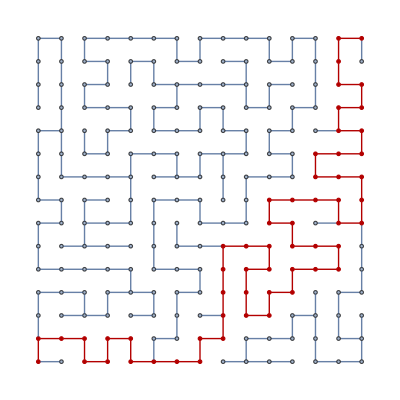
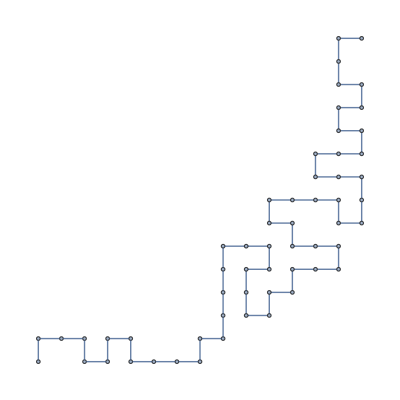
<|start→1,end→225,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→56,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{15,15}]
```

### Scope

Solve a rectangular maze. Note that RandomMaze only supports square mazes.

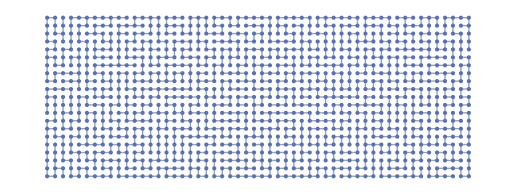
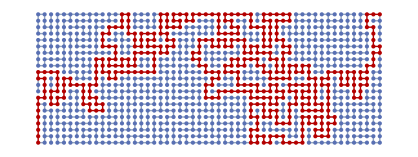
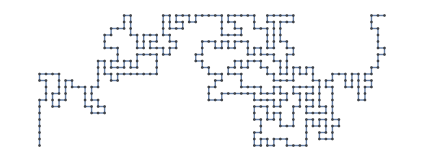
<|start→1,end→1134,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→403,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{21,54}]
```

Solve a medium size maze:

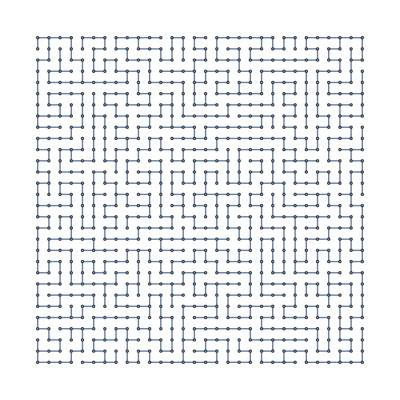
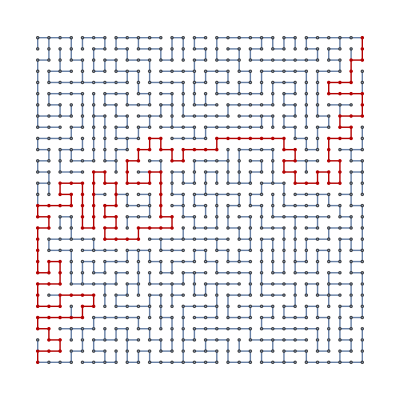
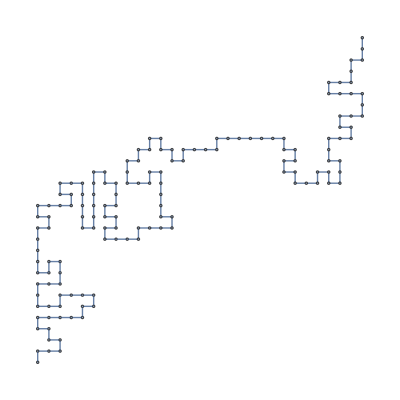
<|start→1,end→900,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→144,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{30,30}]
```

Solve a big maze:

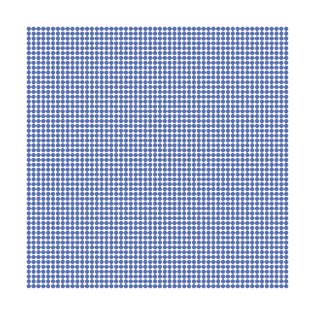
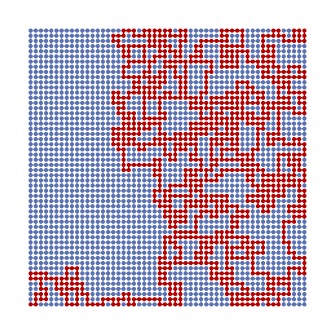
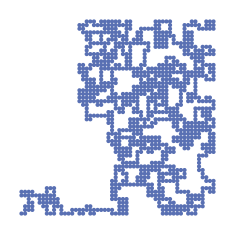
<|start→1,end→2916,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→1084,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{54,54}]
```

Solve a really big maze:

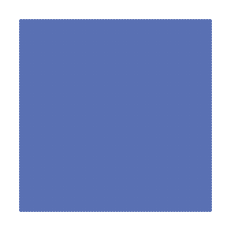
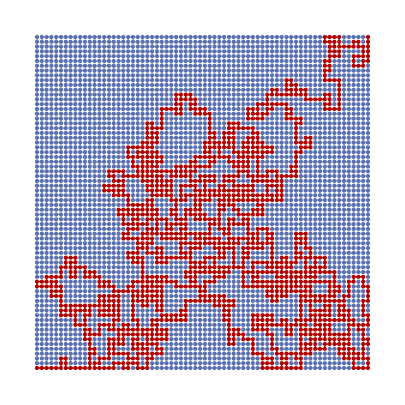
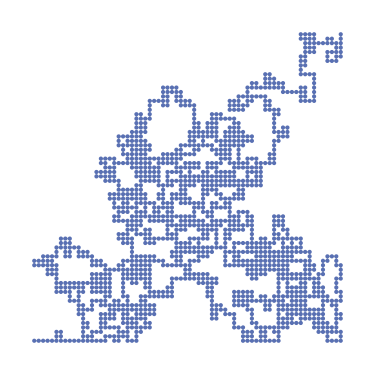
<|start→1,end→4900,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→1554,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{70,70}]
```

### Applications

Find dead ends:

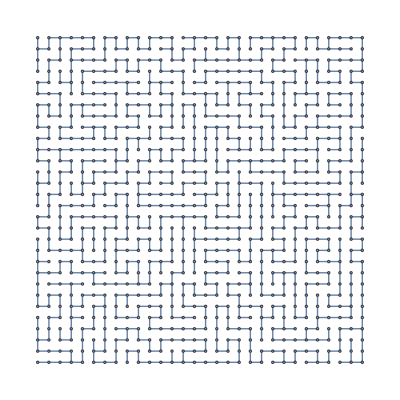
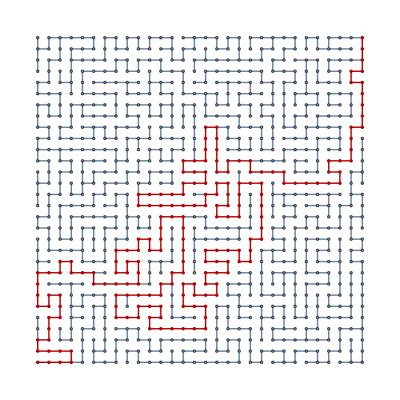
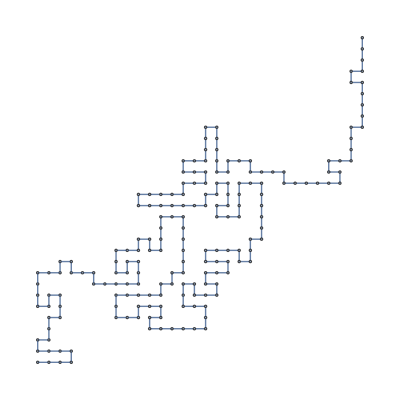
<|start→1,end→900,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→186,shortest-path-subgraph→-Graphics-|>

```mathematica
data=FindRandomGridMazeSolution[{30,30}]
```

Iconized data's shortest path:

```mathematica
data["shortest-path"]
```

Normal:

```mathematica
First[data["shortest-path"]]
```

{1,31,61,91,92,62,32,2,3,33,34,35,65,66,67,37,36,6,7,8,9,39,69,70,100,99,129,159,158,188,218,248,278,279,280,250,249,219,220,221,251,281,282,312,311,341,342,343,344,374,404,403,402,401,400,399,369,368,338,337,307,277,247,217,216,215,245,275,276,306,336,335,305,304,334,364,394,424,454,455,456,426,396,397,398,428,427,457,487,488,458,459,489,519,520,490,460,461,491,521,551,550,580,581,582,612,613,614,615,616,617,587,557,556,555,554,524,494,495,525,526,527,497,496,466,465,435,405,375,345,315,285,286,316,346,376,406,407,437,467,468,438,408,409,439,469,470,471,472,502,501,500,499,498,528,529,559,589,588,618,648,678,677,707,737,767,797,827,828,798,799,829,859,860,861,862,892,893,894,895,896,866,867,897,898,899,900}

```mathematica
Position[Extract[VertexDegree[data["solved-maze"]],Map[{#}&,First[data["shortest-path"]]]],3]
```

{{4},{9},{21},{28},{33},{40},{51},{58},{63},{113},{125},{133},{145},{150},{158},{185}}

```mathematica
data=FindRandomGridMazeSolution[{80,80}];
```

```mathematica
VertexDegree[data["solved-maze"]]
```

4

```mathematica
?VertexDegree
```

Find a solution to a random 20 by 30 maze:

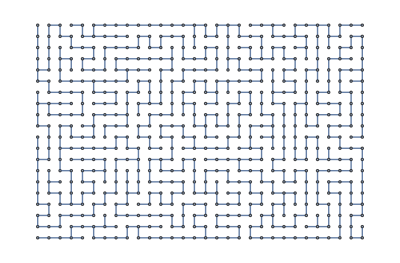
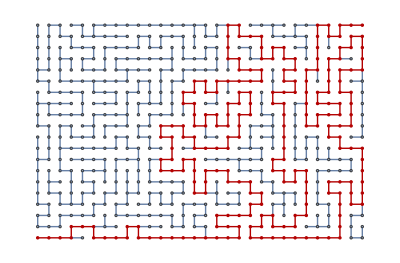
<|maze→-Graphics-,solved-maze→-Graphics-|>

```mathematica
FindRandomMazeSolution[{20,30}]
```

Find a solution to a random 50 by 60 maze:

```mathematica
FindRandomMazeSolution[{50,60}]
```

-Graphics-

Find a solution to a random 60 by 70 maze:

```mathematica
FindRandomMazeSolution[{60,70}]
```

-Graphics-

Solve a random 70 by 80 maze:

```mathematica
FindRandomMazeSolution[{70,80}]
```

-Graphics-

## Source & Additional Information

### Contributed By

Peter Cullen Burbery

### Keywords

mazes

graph algorithms

fun

### Categories

Cloud & Deployment
 External Interfaces & Connections
 Graphs & Networks
 Knowledge Representation & Natural Language
 Repository Tools
 Strings & Text
 User Interface Construction |  Core Language & Structure
 Financial Data & Computation
 Higher Mathematical Computation
 Machine Learning
 Scientific and Medical Data & Computation
 Symbolic & Numeric Computation
 Visualization & Graphics |  Data Manipulation & Analysis
 Geographic Data & Computation
 Images
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 System Operation & Setup
 Wolfram Physics Project |  Engineering Data & Computation
 Geometry
 Just For Fun
 Programming Utilities
 Sound & Video
 Time-Related Computation

### Related Symbols

FindShortestPath

### Related Resource Objects

RandomMaze

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.1+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.